```mathematica
ClearAll["Global`*"]
```

```mathematica
Residue[ (Zeta[s]^2)x^s/s,{s,1}]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
Residue[ (( 1/Zeta[s])) x^s s^(-1),{s,ZetaZero[1]}]/.ZetaZero[1]->z
```

x^z/(z Zeta'[z])

```mathematica
Residue[ Zeta[s],{s,1}]
```

1

```mathematica
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=(Sum[bins[z,a] D2[n,a],{a,0,Log[2,n]}])
gg[n_,z_] := Expand[FullSimplify[(DD[n,z+1]-1)/(z+1)]]
Dhyp[n_,k_,a_]:=Dhyp[n,k,a]=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
DDD[n_,z_]:=Expand[Sum[bins[z,a] Dhyp[n,a,2],{a,0,Log[2,n]}]]
DDD2[n_,z_]:=Sum[bins[z,a] Dhyp[n,a,2],{a,0,Log[2,n]}]
ggr[n_,z_] := Expand[FullSimplify[(DDD[n,z+1]-1)/(z+1)]]
ggr2[n_,z_] := FullSimplify[(DDD[n,z+1]-1)/(z+1)]
ggr3[n_,z_] := FullSimplify[(DDD[n,z]-1)/(z)]
ggr3a[n_,z_] := FullSimplify[(DDD[n,z])/(z)]
ggr3b[n_,z_] := FullSimplify[(DDD[n,z]-1)]
ggr3e[n_,z_] := FullSimplify[(DDD[n,z])]
ggr3f[n_,z_] := FullSimplify[(DDD[n,z+1])]
ggr4[n_,z_] := FullSimplify[(DDD[n,z-1]-1)/(z-1)]
D2z[n_,k_,s_]:=D2z[n,k]=Sum[ j^-s D2z[Floor[n/j],k-1,s],{j,2,n}];D2z[n_,0,s_]:=1
DDz[n_,z_,s_]:=(Sum[bins[z,a] D2z[n,a,s],{a,0,Log[2,n]}])
ggz[n_,z_,s_] := Expand[FullSimplify[(DDz[n,z+1,s]-1)/(z+1)]]
DDa[n_,z_]:=(Sum[bins[z,a] D2a[n,a],{a,0,Log[2,n]}])
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
DDa[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
```

```mathematica
DD[100,0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
Residue[gg[100,s]/s^3 ,{s,0}]
```

3167/90

```mathematica
Limit[gg[100,z],z->-1]
```

428/15

```mathematica
Limit[ggz[100,z,0],z->-1]
```

428/15

```mathematica
Table[{n, FullSimplify[Residue[DD[n,s]/s^2 ,{s,0}]]},{n,1,100}]//TableForm
```

1 | 0
2 | 1
3 | 2
4 | 5/2
5 | 7/2
6 | 7/2
7 | 9/2
8 | 29/6
9 | 16/3
10 | 16/3
11 | 19/3
12 | 19/3
13 | 22/3
14 | 22/3
15 | 22/3
16 | 91/12
17 | 103/12
18 | 103/12
19 | 115/12
20 | 115/12
21 | 115/12
22 | 115/12
23 | 127/12
24 | 127/12
25 | 133/12
26 | 133/12
27 | 137/12
28 | 137/12
29 | 149/12
30 | 149/12
31 | 161/12
32 | 817/60
33 | 817/60
34 | 817/60
35 | 817/60
36 | 817/60
37 | 877/60
38 | 877/60
39 | 877/60
40 | 877/60
41 | 937/60
42 | 937/60
43 | 997/60
44 | 997/60
45 | 997/60
46 | 997/60
47 | 1057/60
48 | 1057/60
49 | 1087/60
50 | 1087/60
51 | 1087/60
52 | 1087/60
53 | 1147/60
54 | 1147/60
55 | 1147/60
56 | 1147/60
57 | 1147/60
58 | 1147/60
59 | 1207/60
60 | 1207/60
61 | 1267/60
62 | 1267/60
63 | 1267/60
64 | 1277/60
65 | 1277/60
66 | 1277/60
67 | 1337/60
68 | 1337/60
69 | 1337/60
70 | 1337/60
71 | 1397/60
72 | 1397/60
73 | 1457/60
74 | 1457/60
75 | 1457/60
76 | 1457/60
77 | 1457/60
78 | 1457/60
79 | 1517/60
80 | 1517/60
81 | 383/15
82 | 383/15
83 | 398/15
84 | 398/15
85 | 398/15
86 | 398/15
87 | 398/15
88 | 398/15
89 | 413/15
90 | 413/15
91 | 413/15
92 | 413/15
93 | 413/15
94 | 413/15
95 | 413/15
96 | 413/15
97 | 428/15
98 | 428/15
99 | 428/15
100 | 428/15

```mathematica
Residue[n^s/(s^3),{s,0}]
```

Log[n]^2/2

```mathematica
Residue[n^s/(s^4),{s,0}]
```

Log[n]^3/6

```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
```

```mathematica
Residue[DD[100,s]/s^2 ,{s,0}]
```

428/15

```mathematica
P[100,1]
```

428/15

```mathematica
Residue[DD[100,s]/s^3,{s,0}]
```

16289/360

```mathematica
P[100,2]/2
```

16289/360

```mathematica
Residue[DD[100,s]/s^4,{s,0}]
```

331/16

```mathematica
P[100,3]/6
```

331/16

```mathematica
f[x_] := x^4
```

```mathematica
Residue[ f[n]/s^3,{s,0}]
```

0

```mathematica
da[ n_, z_] := Sum[ z^k Residue[DD[100,m]/m^(k+1),{m,0}],{k,0,Log[2,n]}]
```

```mathematica
da[100,2]
```

482

```mathematica
Limit[ DD[100,z]/z ,z->0]
```

∞

```mathematica
Residue[ Zeta[s] s^2,{s,1}]
```

1

```mathematica
Series[ Zeta[s],{s,0,20}]
```

-1/2-1/2 Log[2 π] s+1/48 (12 EulerGamma^2-π^2-12 Log[2]^2-24 Log[2] Log[π]-12 Log[π]^2+24 StieltjesGamma[1]) s^2+1/48 (8 EulerGamma^3+12 EulerGamma^2 Log[2 π]-π^2 Log[2 π]-4 Log[2 π]^3+24 EulerGamma StieltjesGamma[1]+24 Log[2 π] StieltjesGamma[1]+12 StieltjesGamma[2]-8 Zeta[3]) s^3+1/24 Zeta^(4)[0] s^4+1/120 Zeta^(5)[0] s^5+1/720 Zeta^(6)[0] s^6+(Zeta^(7)[0] s^7)/5040+(Zeta^(8)[0] s^8)/40320+(Zeta^(9)[0] s^9)/362880+(Zeta^(10)[0] s^10)/3628800+(Zeta^(11)[0] s^11)/39916800+(Zeta^(12)[0] s^12)/479001600+(Zeta^(13)[0] s^13)/6227020800+(Zeta^(14)[0] s^14)/87178291200+(Zeta^(15)[0] s^15)/1307674368000+(Zeta^(16)[0] s^16)/20922789888000+(Zeta^(17)[0] s^17)/355687428096000+(Zeta^(18)[0] s^18)/6402373705728000+(Zeta^(19)[0] s^19)/121645100408832000+(Zeta^(20)[0] s^20)/2432902008176640000+O[s]^21

```mathematica
Zeta''[0]
```

EulerGamma^2/2-π^2/24-1/2 (Log[2]+Log[π])^2+StieltjesGamma[1]

```mathematica
Integrate[DD[100,z],z]
```

z+(214 z^2)/15+(16289 z^3)/1080+(331 z^4)/64+(611 z^5)/720+(67 z^6)/1440+z^7/720

```mathematica
Expand[DD[100,z]]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
gg[1000,z]
```

999+(103337 z)/72+(1647349 z^2)/2016+(5439209 z^3)/22680+(14163823 z^4)/362880+(1301627 z^5)/362880+(64843 z^6)/362880+(1853 z^7)/362880+z^8/36288

```mathematica
(List@@NRoots[ gg[100,x]==0,x][[All,2]])
```

{-12.1997-12.3983 ⅈ,-12.1997+12.3983 ⅈ,-3.65742-1.85785 ⅈ,-3.65742+1.85785 ⅈ,-2.}

```mathematica
vv:= {-12.199718313735843-12.398284753324177 ⅈ,-12.199718313735843+12.398284753324177 ⅈ,-3.6574245434070125-1.8578482376600203 ⅈ,-3.6574245434070125+1.8578482376600203 ⅈ,-2.}
```

```mathematica
99 Product[ 1+1/j,{j,vv}]
```

28.5333+0. ⅈ

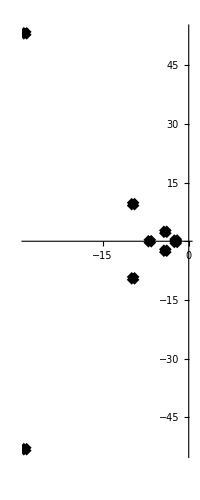

```mathematica
RootLocusPlot[1/Expand[gg[1600,x]],{k,0,1},FeedbackType->None]
```

```mathematica
(List@@NRoots[ DD[100,x]==0,x][[All,2]])
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
(1+3/(List@@NRoots[ gg[200,x]==0,x][[All,2]]))
```

{0.92523+0.0922223 ⅈ,0.92523-0.0922223 ⅈ,0.593448+0.280651 ⅈ,0.593448-0.280651 ⅈ,-0.247394+0.366558 ⅈ,-0.247394-0.366558 ⅈ}

```mathematica
( Product[ 1+2/j,{j,vv}])
```

0.+0. ⅈ

```mathematica
(99 Product[ 1-2/j,{j,vv}])3+1
```

1471.+3.29736×10^-14 ⅈ

```mathematica
(99 Product[ 1+2/j,{j,vv}])(-1)+1
```

1.+0. ⅈ

```mathematica
(Sum[ -1/j,{j,vv}])
```

1.01532+0. ⅈ

```mathematica
Table[{n,Expand[Roots[ Expand[gg[n,x]]==0,x]]},{n,2,32}]//TableForm
```

```mathematica
Table[{n,NRoots[gg[n,x]==0,x]},{n,2,210}]//TableForm
```

NRoots::nnumeq: False is expected to be a polynomial equation in the variable x with numeric coefficients.

2 | NRoots[False,x]
3 | NRoots[False,x]
4 | x==-6.
5 | x==-8.
6 | x==-3.33333
7 | x==-4.
8 | x==-9.64575||x==-4.35425
9 | x==-13.4244||x==-3.57557
10 | x==-20.3459||x==-2.6541
11 | x==-20.||x==-3.
12 | x==-4.-0.707107 ⅈ||x==-4.+0.707107 ⅈ
13 | x==-4.-1.41421 ⅈ||x==-4.+1.41421 ⅈ
14 | x==-6.5||x==-3.
15 | x==-8.54138||x==-2.45862
16 | x==-11.2727-4.42556 ⅈ||x==-11.2727+4.42556 ⅈ||x==-2.45468
17 | x==-11.1434-4.1661 ⅈ||x==-11.1434+4.1661 ⅈ||x==-2.71316
18 | x==-29.3693||x==-4.63068||x==-3.
19 | x==-29.406||x==-3.797-0.523141 ⅈ||x==-3.797+0.523141 ⅈ
20 | x==-42.8546||x==-3.07271-1.09503 ⅈ||x==-3.07271+1.09503 ⅈ
21 | x==-42.2094||x==-3.79063||x==-3.
22 | x==-41.5406||x==-5.06306||x==-2.39632
23 | x==-41.5574||x==-4.79027||x==-2.65232
24 | x==-5.96489-2.40103 ⅈ||x==-5.96489+2.40103 ⅈ||x==-2.67023
25 | x==-6.00599-2.90531 ⅈ||x==-6.00599+2.90531 ⅈ||x==-2.58802
26 | x==-6.14747-3.77731 ⅈ||x==-6.14747+3.77731 ⅈ||x==-2.30506
27 | x==-6.55036-3.37202 ⅈ||x==-6.55036+3.37202 ⅈ||x==-2.29929
28 | x==-9.80776||x==-5.65592||x==-2.33632
29 | x==-9.95434||x==-5.29649||x==-2.54917
30 | x==-17.1815||x==-2.70926-0.872723 ⅈ||x==-2.70926+0.872723 ⅈ
31 | x==-17.2042||x==-2.69788-1.04473 ⅈ||x==-2.69788+1.04473 ⅈ
32 | x==-16.8095-12.8145 ⅈ||x==-16.8095+12.8145 ⅈ||x==-2.69051-1.04288 ⅈ||x==-2.69051+1.04288 ⅈ
33 | x==-16.6177-12.6273 ⅈ||x==-16.6177+12.6273 ⅈ||x==-2.88226-0.71277 ⅈ||x==-2.88226+0.71277 ⅈ
34 | x==-16.4136-12.4346 ⅈ||x==-16.4136+12.4346 ⅈ||x==-3.51862||x==-2.65418
35 | x==-16.1951-12.2362 ⅈ||x==-16.1951+12.2362 ⅈ||x==-4.31448||x==-2.29524
36 | x==-55.9842||x==-5.36265-1.99868 ⅈ||x==-5.36265+1.99868 ⅈ||x==-2.29053
37 | x==-55.9833||x==-5.2723-1.84864 ⅈ||x==-5.2723+1.84864 ⅈ||x==-2.47211
38 | x==-56.0311||x==-5.35957-2.54895 ⅈ||x==-5.35957+2.54895 ⅈ||x==-2.24977
39 | x==-56.0787||x==-5.40778-3.06127 ⅈ||x==-5.40778+3.06127 ⅈ||x==-2.10574
40 | x==-77.9886||x==-4.45185-2.94149 ⅈ||x==-4.45185+2.94149 ⅈ||x==-2.10769
41 | x==-77.9883||x==-4.39383-2.89281 ⅈ||x==-4.39383+2.89281 ⅈ||x==-2.22402
42 | x==-76.2124||x==-6.05457||x==-4.1856||x==-2.54741
43 | x==-76.2121||x==-6.27489||x==-3.51301||x==-3.
44 | x==-75.3||x==-7.93271||x==-2.88365-0.56828 ⅈ||x==-2.88365+0.56828 ⅈ
45 | x==-74.3616||x==-9.26209||x==-2.68818-0.663199 ⅈ||x==-2.68818+0.663199 ⅈ
46 | x==-74.3879||x==-8.89038||x==-3.||x==-2.72176
47 | x==-74.3875||x==-8.94002||x==-2.83624-0.506135 ⅈ||x==-2.83624+0.506135 ⅈ
48 | x==-8.73692-5.99905 ⅈ||x==-8.73692+5.99905 ⅈ||x==-2.84642-0.516416 ⅈ||x==-2.84642+0.516416 ⅈ
49 | x==-8.65424-5.92882 ⅈ||x==-8.65424+5.92882 ⅈ||x==-2.9291-0.379417 ⅈ||x==-2.9291+0.379417 ⅈ
50 | x==-8.84235-6.87153 ⅈ||x==-8.84235+6.87153 ⅈ||x==-2.74098-0.549257 ⅈ||x==-2.74098+0.549257 ⅈ
51 | x==-8.68808-6.76931 ⅈ||x==-8.68808+6.76931 ⅈ||x==-3.26792||x==-2.52258
52 | x==-8.85076-7.58847 ⅈ||x==-8.85076+7.58847 ⅈ||x==-2.73258-0.193384 ⅈ||x==-2.73258+0.193384 ⅈ
53 | x==-8.86431-7.58559 ⅈ||x==-8.86431+7.58559 ⅈ||x==-2.71903-0.497377 ⅈ||x==-2.71903+0.497377 ⅈ
54 | x==-10.5282-5.1973 ⅈ||x==-10.5282+5.1973 ⅈ||x==-2.72179-0.530173 ⅈ||x==-2.72179+0.530173 ⅈ
55 | x==-10.3716-5.00381 ⅈ||x==-10.3716+5.00381 ⅈ||x==-3.25357||x==-2.50318
56 | x==-15.4864||x==-8.5194||x==-3.30432||x==-2.52319
57 | x==-15.7351||x==-7.77056||x==-4.0857||x==-2.24197
58 | x==-15.9594||x==-6.68146||x==-5.09353||x==-2.09893
59 | x==-15.945||x==-6.93096||x==-4.74544||x==-2.21188
60 | x==-30.4075||x==-3.61536-2.14655 ⅈ||x==-3.61536+2.14655 ⅈ||x==-2.1951
61 | x==-30.4065||x==-3.55952-2.10496 ⅈ||x==-3.55952+2.10496 ⅈ||x==-2.30777
62 | x==-30.4353||x==-3.61081-2.31952 ⅈ||x==-3.61081+2.31952 ⅈ||x==-2.17639
63 | x==-30.0198||x==-3.81327-2.08473 ⅈ||x==-3.81327+2.08473 ⅈ||x==-2.187
64 | x==-23.1014-23.8156 ⅈ||x==-23.1014+23.8156 ⅈ||x==-3.80529-2.08901 ⅈ||x==-3.80529+2.08901 ⅈ||x==-2.18658
65 | x==-23.1175-23.8118 ⅈ||x==-23.1175+23.8118 ⅈ||x==-3.84181-2.31104 ⅈ||x==-3.84181+2.31104 ⅈ||x==-2.08139
66 | x==-22.6567-23.5126 ⅈ||x==-22.6567+23.5126 ⅈ||x==-4.23649-1.37208 ⅈ||x==-4.23649+1.37208 ⅈ||x==-2.21353
67 | x==-22.6565-23.5131 ⅈ||x==-22.6565+23.5131 ⅈ||x==-4.16816-1.25972 ⅈ||x==-4.16816+1.25972 ⅈ||x==-2.35069
68 | x==-22.4219-23.3619 ⅈ||x==-22.4219+23.3619 ⅈ||x==-4.3811-0.15363 ⅈ||x==-4.3811+0.15363 ⅈ||x==-2.39405
69 | x==-22.4393-23.3567 ⅈ||x==-22.4393+23.3567 ⅈ||x==-4.45888-1.13933 ⅈ||x==-4.45888+1.13933 ⅈ||x==-2.20354
70 | x==-21.9254-23.062 ⅈ||x==-21.9254+23.062 ⅈ||x==-6.76899||x==-2.69014-0.106337 ⅈ||x==-2.69014+0.106337 ⅈ
71 | x==-21.9251-23.0626 ⅈ||x==-21.9251+23.0626 ⅈ||x==-6.82439||x==-2.66269-0.451118 ⅈ||x==-2.66269+0.451118 ⅈ
72 | x==-96.1136||x==-7.27409-4.44394 ⅈ||x==-7.27409+4.44394 ⅈ||x==-2.66913-0.442295 ⅈ||x==-2.66913+0.442295 ⅈ
73 | x==-96.1136||x==-7.2961-4.44609 ⅈ||x==-7.2961+4.44609 ⅈ||x==-2.64712-0.61742 ⅈ||x==-2.64712+0.61742 ⅈ
74 | x==-96.1126||x==-7.16026-4.33243 ⅈ||x==-7.16026+4.33243 ⅈ||x==-2.78345-0.245505 ⅈ||x==-2.78345+0.245505 ⅈ
75 | x==-96.1592||x==-7.26186-4.8925 ⅈ||x==-7.26186+4.8925 ⅈ||x==-2.65856-0.398483 ⅈ||x==-2.65856+0.398483 ⅈ
76 | x==-96.2057||x==-7.33313-5.3758 ⅈ||x==-7.33313+5.3758 ⅈ||x==-2.56403-0.463693 ⅈ||x==-2.56403+0.463693 ⅈ
77 | x==-96.2047||x==-7.23305-5.30245 ⅈ||x==-7.23305+5.30245 ⅈ||x==-2.83367||x==-2.49555
78 | x==-96.2984||x==-7.42509-6.19962 ⅈ||x==-7.42509+6.19962 ⅈ||x==-2.42572-0.518439 ⅈ||x==-2.42572+0.518439 ⅈ
79 | x==-96.2984||x==-7.43527-6.19822 ⅈ||x==-7.43527+6.19822 ⅈ||x==-2.41554-0.623762 ⅈ||x==-2.41554+0.623762 ⅈ
80 | x==-128.657||x==-6.25813-5.6474 ⅈ||x==-6.25813+5.6474 ⅈ||x==-2.41341-0.630298 ⅈ||x==-2.41341+0.630298 ⅈ
81 | x==-128.408||x==-6.38319-5.60717 ⅈ||x==-6.38319+5.60717 ⅈ||x==-2.41298-0.625857 ⅈ||x==-2.41298+0.625857 ⅈ
82 | x==-128.407||x==-6.30608-5.56445 ⅈ||x==-6.30608+5.56445 ⅈ||x==-2.49028-0.468879 ⅈ||x==-2.49028+0.468879 ⅈ
83 | x==-128.407||x==-6.31715-5.56085 ⅈ||x==-6.31715+5.56085 ⅈ||x==-2.47921-0.587362 ⅈ||x==-2.47921+0.587362 ⅈ
84 | x==-125.2||x==-7.7844-2.36701 ⅈ||x==-7.7844+2.36701 ⅈ||x==-2.61555-0.607586 ⅈ||x==-2.61555+0.607586 ⅈ
85 | x==-125.2||x==-7.63324-2.08383 ⅈ||x==-7.63324+2.08383 ⅈ||x==-2.76692-0.244581 ⅈ||x==-2.76692+0.244581 ⅈ
86 | x==-125.199||x==-7.43383-1.69746 ⅈ||x==-7.43383+1.69746 ⅈ||x==-3.59362||x==-2.33948
87 | x==-125.199||x==-7.10589-0.982123 ⅈ||x==-7.10589+0.982123 ⅈ||x==-4.41001||x==-2.1794
88 | x==-124.105||x==-10.5034||x==-4.60437-0.904495 ⅈ||x==-4.60437+0.904495 ⅈ||x==-2.18246
89 | x==-124.105||x==-10.4818||x==-4.55637-0.644862 ⅈ||x==-4.55637+0.644862 ⅈ||x==-2.30005
90 | x==-120.625||x==-16.2611||x==-3.42106-1.63576 ⅈ||x==-3.42106+1.63576 ⅈ||x==-2.27194
91 | x==-120.624||x==-16.3057||x==-3.4572-1.82538 ⅈ||x==-3.4572+1.82538 ⅈ||x==-2.15554
92 | x==-120.654||x==-15.9803||x==-3.60076-1.65521 ⅈ||x==-3.60076+1.65521 ⅈ||x==-2.16372
93 | x==-120.654||x==-16.0278||x==-3.62335-1.84559 ⅈ||x==-3.62335+1.84559 ⅈ||x==-2.0716
94 | x==-120.653||x==-16.0745||x==-3.63601-2.01049 ⅈ||x==-3.63601+2.01049 ⅈ||x==-2.
95 | x==-120.653||x==-16.1207||x==-3.64243-2.15752 ⅈ||x==-3.64243+2.15752 ⅈ||x==-1.94155
96 | x==-12.2338-11.283 ⅈ||x==-12.2338+11.283 ⅈ||x==-3.65266-2.19783 ⅈ||x==-3.65266+2.19783 ⅈ||x==-1.94138
97 | x==-12.2331-11.2843 ⅈ||x==-12.2331+11.2843 ⅈ||x==-3.62405-2.16584 ⅈ||x==-3.62405+2.16584 ⅈ||x==-2.
98 | x==-12.074-11.1913 ⅈ||x==-12.074+11.1913 ⅈ||x==-3.78317-2.02334 ⅈ||x==-3.78317+2.02334 ⅈ||x==-2.
99 | x==-11.9064-11.0997 ⅈ||x==-11.9064+11.0997 ⅈ||x==-3.95075-1.84742 ⅈ||x==-3.95075+1.84742 ⅈ||x==-2.
100 | x==-12.1997-12.3983 ⅈ||x==-12.1997+12.3983 ⅈ||x==-3.65742-1.85785 ⅈ||x==-3.65742+1.85785 ⅈ||x==-2.
101 | x==-12.1993-12.3994 ⅈ||x==-12.1993+12.3994 ⅈ||x==-3.62427-1.81947 ⅈ||x==-3.62427+1.81947 ⅈ||x==-2.06708
102 | x==-11.8988-12.2682 ⅈ||x==-11.8988+12.2682 ⅈ||x==-3.87396-1.17951 ⅈ||x==-3.87396+1.17951 ⅈ||x==-2.16885
103 | x==-11.8984-12.2694 ⅈ||x==-11.8984+12.2694 ⅈ||x==-3.82066-1.08726 ⅈ||x==-3.82066+1.08726 ⅈ||x==-2.27611
104 | x==-12.0439-13.0382 ⅈ||x==-12.0439+13.0382 ⅈ||x==-3.67259-1.11924 ⅈ||x==-3.67259+1.11924 ⅈ||x==-2.28126
105 | x==-11.7617-12.9332 ⅈ||x==-11.7617+12.9332 ⅈ||x==-4.87028||x==-2.66029-0.331598 ⅈ||x==-2.66029+0.331598 ⅈ
106 | x==-11.7773-12.9237 ⅈ||x==-11.7773+12.9237 ⅈ||x==-4.34542||x==-3.47444||x==-2.33977
107 | x==-11.7772-12.9248 ⅈ||x==-11.7772+12.9248 ⅈ||x==-4.54426||x==-3.||x==-2.6157
108 | x==-15.7224-4.6639 ⅈ||x==-15.7224+4.6639 ⅈ||x==-5.23562||x==-3.||x==-2.60534
109 | x==-15.7178-4.66164 ⅈ||x==-15.7178+4.66164 ⅈ||x==-5.35828||x==-2.74592-0.416127 ⅈ||x==-2.74592+0.416127 ⅈ
110 | x==-14.9535-3.19075 ⅈ||x==-14.9535+3.19075 ⅈ||x==-7.49518||x==-2.44179-0.660187 ⅈ||x==-2.44179+0.660187 ⅈ
111 | x==-15.0553-3.31693 ⅈ||x==-15.0553+3.31693 ⅈ||x==-7.10072||x==-2.53718-0.516845 ⅈ||x==-2.53718+0.516845 ⅈ
112 | x==-25.6693||x==-7.91464-1.91422 ⅈ||x==-7.91464+1.91422 ⅈ||x==-2.53645-0.52387 ⅈ||x==-2.53645+0.52387 ⅈ
113 | x==-25.6699||x==-7.93896-1.95197 ⅈ||x==-7.93896+1.95197 ⅈ||x==-2.51183-0.636536 ⅈ||x==-2.51183+0.636536 ⅈ
114 | x==-26.0218||x==-7.9481-3.46931 ⅈ||x==-7.9481+3.46931 ⅈ||x==-2.3267-0.724836 ⅈ||x==-2.3267+0.724836 ⅈ
115 | x==-26.0083||x==-7.88404-3.33549 ⅈ||x==-7.88404+3.33549 ⅈ||x==-2.39754-0.635499 ⅈ||x==-2.39754+0.635499 ⅈ
116 | x==-26.1684||x==-7.84803-3.81216 ⅈ||x==-7.84803+3.81216 ⅈ||x==-2.35348-0.6317 ⅈ||x==-2.35348+0.6317 ⅈ
117 | x==-26.3232||x==-7.80893-4.22033 ⅈ||x==-7.80893+4.22033 ⅈ||x==-2.31516-0.626754 ⅈ||x==-2.31516+0.626754 ⅈ
118 | x==-26.3107||x==-7.75348-4.12558 ⅈ||x==-7.75348+4.12558 ⅈ||x==-2.37689-0.529162 ⅈ||x==-2.37689+0.529162 ⅈ
119 | x==-26.2981||x==-7.69346-4.02616 ⅈ||x==-7.69346+4.02616 ⅈ||x==-2.4432-0.38961 ⅈ||x==-2.4432+0.38961 ⅈ
120 | x==-49.1479||x==-4.82762-4.1295 ⅈ||x==-4.82762+4.1295 ⅈ||x==-2.4556-0.375248 ⅈ||x==-2.4556+0.375248 ⅈ
121 | x==-49.1473||x==-4.80076-4.11365 ⅈ||x==-4.80076+4.11365 ⅈ||x==-2.48274-0.345415 ⅈ||x==-2.48274+0.345415 ⅈ
122 | x==-49.1461||x==-4.73355-4.08876 ⅈ||x==-4.73355+4.08876 ⅈ||x==-2.73083||x==-2.37021
123 | x==-49.145||x==-4.66345-4.06658 ⅈ||x==-4.66345+4.06658 ⅈ||x==-3.06978||x==-2.1726
124 | x==-49.172||x==-4.71161-4.23507 ⅈ||x==-4.71161+4.23507 ⅈ||x==-2.93454||x==-2.18453
125 | x==-49.1806||x==-4.70808-4.28063 ⅈ||x==-4.70808+4.28063 ⅈ||x==-2.93594||x==-2.18157
126 | x==-47.8377||x==-5.22182-3.27114 ⅈ||x==-5.22182+3.27114 ⅈ||x==-3.2646||x==-2.16835
127 | x==-47.8377||x==-5.24292-3.26705 ⅈ||x==-5.24292+3.26705 ⅈ||x==-3.1026||x==-2.28813
128 | x==-30.0652-38.1714 ⅈ||x==-30.0652+38.1714 ⅈ||x==-5.23968-3.27773 ⅈ||x==-5.23968+3.27773 ⅈ||x==-3.10252||x==-2.28765
129 | x==-30.0651-38.1721 ⅈ||x==-30.0651+38.1721 ⅈ||x==-5.13151-3.2272 ⅈ||x==-5.13151+3.2272 ⅈ||x==-3.45404||x==-2.15272
130 | x==-30.0948-38.1571 ⅈ||x==-30.0948+38.1571 ⅈ||x==-5.36023-3.73814 ⅈ||x==-5.36023+3.73814 ⅈ||x==-2.71944||x==-2.37049
131 | x==-30.0948-38.1571 ⅈ||x==-30.0948+38.1571 ⅈ||x==-5.37487-3.73542 ⅈ||x==-5.37487+3.73542 ⅈ||x==-2.53033-0.270259 ⅈ||x==-2.53033+0.270259 ⅈ
132 | x==-29.3695-37.8081 ⅈ||x==-29.3695+37.8081 ⅈ||x==-5.94649-2.16528 ⅈ||x==-5.94649+2.16528 ⅈ||x==-2.78963||x==-2.57835
133 | x==-29.3694-37.8089 ⅈ||x==-29.3694+37.8089 ⅈ||x==-5.79002-1.99311 ⅈ||x==-5.79002+1.99311 ⅈ||x==-3.41331||x==-2.2678
134 | x==-29.3693-37.8096 ⅈ||x==-29.3693+37.8096 ⅈ||x==-5.55763-1.78329 ⅈ||x==-5.55763+1.78329 ⅈ||x==-4.||x==-2.14607
135 | x==-29.1278-37.6917 ⅈ||x==-29.1278+37.6917 ⅈ||x==-5.89714||x==-5.||x==-4.69908||x==-2.14812
136 | x==-28.8813-37.5758 ⅈ||x==-28.8813+37.5758 ⅈ||x==-7.68743||x==-4.19983-0.829268 ⅈ||x==-4.19983+0.829268 ⅈ||x==-2.15023
137 | x==-28.8813-37.5758 ⅈ||x==-28.8813+37.5758 ⅈ||x==-7.64831||x==-4.17088-0.599058 ⅈ||x==-4.17088+0.599058 ⅈ||x==-2.24728
138 | x==-28.9125-37.5567 ⅈ||x==-28.9125+37.5567 ⅈ||x==-6.50394-1.82814 ⅈ||x==-6.50394+1.82814 ⅈ||x==-2.5836-0.243084 ⅈ||x==-2.5836+0.243084 ⅈ
139 | x==-28.9124-37.5567 ⅈ||x==-28.9124+37.5567 ⅈ||x==-6.53155-1.85367 ⅈ||x==-6.53155+1.85367 ⅈ||x==-2.556-0.428142 ⅈ||x==-2.556+0.428142 ⅈ
140 | x==-28.1109-37.242 ⅈ||x==-28.1109+37.242 ⅈ||x==-10.2096||x==-4.||x==-2.78432-0.355996 ⅈ||x==-2.78432+0.355996 ⅈ
141 | x==-28.1109-37.2428 ⅈ||x==-28.1109+37.2428 ⅈ||x==-10.287||x==-3.54618-0.746427 ⅈ||x==-3.54618+0.746427 ⅈ||x==-2.39891
142 | x==-28.1109-37.2437 ⅈ||x==-28.1109+37.2437 ⅈ||x==-10.3611||x==-3.59156-1.09581 ⅈ||x==-3.59156+1.09581 ⅈ||x==-2.2341
143 | x==-28.1108-37.2445 ⅈ||x==-28.1108+37.2445 ⅈ||x==-10.4322||x==-3.60659-1.32818 ⅈ||x==-3.60659+1.32818 ⅈ||x==-2.13297
144 | x==-152.703||x==-9.44113-7.65529 ⅈ||x==-9.44113+7.65529 ⅈ||x==-3.64071-1.31265 ⅈ||x==-3.64071+1.31265 ⅈ||x==-2.13292
145 | x==-152.703||x==-9.46705-7.64819 ⅈ||x==-9.46705+7.64819 ⅈ||x==-3.65185-1.49978 ⅈ||x==-3.65185+1.49978 ⅈ||x==-2.0588
146 | x==-152.703||x==-9.49299-7.64148 ⅈ||x==-9.49299+7.64148 ⅈ||x==-3.65531-1.65872 ⅈ||x==-3.65531+1.65872 ⅈ||x==-2.
147 | x==-152.703||x==-9.36711-7.56743 ⅈ||x==-9.36711+7.56743 ⅈ||x==-3.7816-1.5215 ⅈ||x==-3.7816+1.5215 ⅈ||x==-2.
148 | x==-152.702||x==-9.2332-7.49522 ⅈ||x==-9.2332+7.49522 ⅈ||x==-3.91594-1.34837 ⅈ||x==-3.91594+1.34837 ⅈ||x==-2.
149 | x==-152.702||x==-9.23191-7.49756 ⅈ||x==-9.23191+7.49756 ⅈ||x==-3.88772-1.28789 ⅈ||x==-3.88772+1.28789 ⅈ||x==-2.05902
150 | x==-152.828||x==-9.66151-8.91424 ⅈ||x==-9.66151+8.91424 ⅈ||x==-3.39576-1.5139 ⅈ||x==-3.39576+1.5139 ⅈ||x==-2.05704
151 | x==-152.828||x==-9.6609-8.91553 ⅈ||x==-9.6609+8.91553 ⅈ||x==-3.36509-1.47662 ⅈ||x==-3.36509+1.47662 ⅈ||x==-2.1196
152 | x==-152.87||x==-9.70027-9.28907 ⅈ||x==-9.70027+9.28907 ⅈ||x==-3.30427-1.44726 ⅈ||x==-3.30427+1.44726 ⅈ||x==-2.12091
153 | x==-152.869||x==-9.6161-9.24135 ⅈ||x==-9.6161+9.24135 ⅈ||x==-3.3865-1.3364 ⅈ||x==-3.3865+1.3364 ⅈ||x==-2.12563
154 | x==-152.867||x==-9.42357-9.15576 ⅈ||x==-9.42357+9.15576 ⅈ||x==-3.51962-0.788373 ⅈ||x==-3.51962+0.788373 ⅈ||x==-2.24612
155 | x==-152.868||x==-9.43928-9.14853 ⅈ||x==-9.43928+9.14853 ⅈ||x==-3.55867-1.04322 ⅈ||x==-3.55867+1.04322 ⅈ||x==-2.1366
156 | x==-152.994||x==-9.71747-10.2701 ⅈ||x==-9.71747+10.2701 ⅈ||x==-3.22066-1.27222 ⅈ||x==-3.22066+1.27222 ⅈ||x==-2.13013
157 | x==-152.994||x==-9.71722-10.2709 ⅈ||x==-9.71722+10.2709 ⅈ||x==-3.18185-1.23154 ⅈ||x==-3.18185+1.23154 ⅈ||x==-2.20824
158 | x==-152.994||x==-9.72838-10.2659 ⅈ||x==-9.72838+10.2659 ⅈ||x==-3.21414-1.36303 ⅈ||x==-3.21414+1.36303 ⅈ||x==-2.12134
159 | x==-152.994||x==-9.73957-10.2609 ⅈ||x==-9.73957+10.2609 ⅈ||x==-3.23641-1.47788 ⅈ||x==-3.23641+1.47788 ⅈ||x==-2.05442
160 | x==-197.807||x==-8.33599-9.28383 ⅈ||x==-8.33599+9.28383 ⅈ||x==-3.23311-1.48759 ⅈ||x==-3.23311+1.48759 ⅈ||x==-2.05457
161 | x==-197.807||x==-8.34745-9.27648 ⅈ||x==-8.34745+9.27648 ⅈ||x==-3.24894-1.59158 ⅈ||x==-3.24894+1.59158 ⅈ||x==-2.
162 | x==-196.654||x==-8.94511-8.87931 ⅈ||x==-8.94511+8.87931 ⅈ||x==-3.22768-1.6029 ⅈ||x==-3.22768+1.6029 ⅈ||x==-2.
163 | x==-196.654||x==-8.94475-8.88047 ⅈ||x==-8.94475+8.88047 ⅈ||x==-3.20211-1.57572 ⅈ||x==-3.20211+1.57572 ⅈ||x==-2.05187
164 | x==-196.654||x==-8.87163-8.84307 ⅈ||x==-8.87163+8.84307 ⅈ||x==-3.27467-1.49753 ⅈ||x==-3.27467+1.49753 ⅈ||x==-2.05338
165 | x==-196.653||x==-8.70546-8.77824 ⅈ||x==-8.70546+8.77824 ⅈ||x==-3.4037-1.15555 ⅈ||x==-3.4037+1.15555 ⅈ||x==-2.12838
166 | x==-196.653||x==-8.71911-8.77079 ⅈ||x==-8.71911+8.77079 ⅈ||x==-3.42588-1.30617 ⅈ||x==-3.42588+1.30617 ⅈ||x==-2.05672
167 | x==-196.653||x==-8.71881-8.77209 ⅈ||x==-8.71881+8.77209 ⅈ||x==-3.39467-1.26366 ⅈ||x==-3.39467+1.26366 ⅈ||x==-2.11975
168 | x==-191.809||x==-10.9977-4.64931 ⅈ||x==-10.9977+4.64931 ⅈ||x==-3.53847-1.41758 ⅈ||x==-3.53847+1.41758 ⅈ||x==-2.1183
169 | x==-191.809||x==-11.0146-4.65857 ⅈ||x==-11.0146+4.65857 ⅈ||x==-3.52345-1.47704 ⅈ||x==-3.52345+1.47704 ⅈ||x==-2.11455
170 | x==-191.809||x==-10.6846-4.26045 ⅈ||x==-10.6846+4.26045 ⅈ||x==-3.80283-0.824356 ⅈ||x==-3.80283+0.824356 ⅈ||x==-2.21663
171 | x==-191.808||x==-10.5036-4.03785 ⅈ||x==-10.5036+4.03785 ⅈ||x==-4.||x==-3.95483||x==-2.22993
172 | x==-191.808||x==-10.2838-3.783 ⅈ||x==-10.2838+3.783 ⅈ||x==-5.1323||x==-3.24648||x==-2.24602
173 | x==-191.808||x==-10.2757-3.78281 ⅈ||x==-10.2757+3.78281 ⅈ||x==-5.24578||x==-3.||x==-2.39523
174 | x==-191.807||x==-9.37041-3.0915 ⅈ||x==-9.37041+3.0915 ⅈ||x==-7.54603||x==-2.45315-0.411586 ⅈ||x==-2.45315+0.411586 ⅈ
175 | x==-191.806||x==-9.40118||x==-8.48657-3.03156 ⅈ||x==-8.48657+3.03156 ⅈ||x==-2.40963-0.426751 ⅈ||x==-2.40963+0.426751 ⅈ
176 | x==-190.571||x==-13.4252||x==-7.09365-2.69998 ⅈ||x==-7.09365+2.69998 ⅈ||x==-2.40802-0.430641 ⅈ||x==-2.40802+0.430641 ⅈ
177 | x==-190.571||x==-13.3624||x==-7.05617-2.52469 ⅈ||x==-7.05617+2.52469 ⅈ||x==-2.4769-0.259149 ⅈ||x==-2.4769+0.259149 ⅈ
178 | x==-190.571||x==-13.2965||x==-7.01038-2.32211 ⅈ||x==-7.01038+2.32211 ⅈ||x==-2.83123||x==-2.28
179 | x==-190.571||x==-13.302||x==-7.02966-2.35064 ⅈ||x==-7.02966+2.35064 ⅈ||x==-2.5336-0.148857 ⅈ||x==-2.5336+0.148857 ⅈ
180 | x==-182.561||x==-26.7964||x==-4.32342-3.27378 ⅈ||x==-4.32342+3.27378 ⅈ||x==-2.4978-0.17773 ⅈ||x==-2.4978+0.17773 ⅈ
181 | x==-182.561||x==-26.7965||x==-4.33601-3.26876 ⅈ||x==-4.33601+3.26876 ⅈ||x==-2.48516-0.336608 ⅈ||x==-2.48516+0.336608 ⅈ
182 | x==-182.56||x==-26.8667||x==-4.42768-3.52818 ⅈ||x==-4.42768+3.52818 ⅈ||x==-2.35886-0.488277 ⅈ||x==-2.35886+0.488277 ⅈ
183 | x==-182.56||x==-26.864||x==-4.38022-3.50472 ⅈ||x==-4.38022+3.50472 ⅈ||x==-2.40767-0.382808 ⅈ||x==-2.40767+0.382808 ⅈ
184 | x==-182.591||x==-26.5937||x==-4.50479-3.42913 ⅈ||x==-4.50479+3.42913 ⅈ||x==-2.40286-0.390313 ⅈ||x==-2.40286+0.390313 ⅈ
185 | x==-182.591||x==-26.5909||x==-4.45382-3.40358 ⅈ||x==-4.45382+3.40358 ⅈ||x==-2.45524-0.224971 ⅈ||x==-2.45524+0.224971 ⅈ
186 | x==-182.59||x==-26.6629||x==-4.53262-3.65405 ⅈ||x==-4.53262+3.65405 ⅈ||x==-2.34098-0.412285 ⅈ||x==-2.34098+0.412285 ⅈ
187 | x==-182.59||x==-26.6601||x==-4.48923-3.63101 ⅈ||x==-4.48923+3.63101 ⅈ||x==-2.38576-0.291157 ⅈ||x==-2.38576+0.291157 ⅈ
188 | x==-182.589||x==-26.6944||x==-4.50189-3.73721 ⅈ||x==-4.50189+3.73721 ⅈ||x==-2.35621-0.310832 ⅈ||x==-2.35621+0.310832 ⅈ
189 | x==-182.62||x==-26.4213||x==-4.6274-3.66812 ⅈ||x==-4.6274+3.66812 ⅈ||x==-2.35187-0.317315 ⅈ||x==-2.35187+0.317315 ⅈ
190 | x==-182.619||x==-26.4945||x==-4.68038-3.89882 ⅈ||x==-4.68038+3.89882 ⅈ||x==-2.2628-0.43057 ⅈ||x==-2.2628+0.43057 ⅈ
191 | x==-182.619||x==-26.4946||x==-4.68795-3.89689 ⅈ||x==-4.68795+3.89689 ⅈ||x==-2.25517-0.489777 ⅈ||x==-2.25517+0.489777 ⅈ
192 | x==-16.165-18.2884 ⅈ||x==-16.165+18.2884 ⅈ||x==-4.70521-3.97397 ⅈ||x==-4.70521+3.97397 ⅈ||x==-2.25475-0.490671 ⅈ||x==-2.25475+0.490671 ⅈ
193 | x==-16.165-18.2884 ⅈ||x==-16.165+18.2884 ⅈ||x==-4.71292-3.97198 ⅈ||x==-4.71292+3.97198 ⅈ||x==-2.24709-0.543274 ⅈ||x==-2.24709+0.543274 ⅈ
194 | x==-16.1647-18.29 ⅈ||x==-16.1647+18.29 ⅈ||x==-4.6759-3.9488 ⅈ||x==-4.6759+3.9488 ⅈ||x==-2.28443-0.47909 ⅈ||x==-2.28443+0.47909 ⅈ
195 | x==-16.1999-18.2708 ⅈ||x==-16.1999+18.2708 ⅈ||x==-4.71583-4.17293 ⅈ||x==-4.71583+4.17293 ⅈ||x==-2.20928-0.537067 ⅈ||x==-2.20928+0.537067 ⅈ
196 | x==-15.9925-18.1742 ⅈ||x==-15.9925+18.1742 ⅈ||x==-4.92235-4.03062 ⅈ||x==-4.92235+4.03062 ⅈ||x==-2.21019-0.542236 ⅈ||x==-2.21019+0.542236 ⅈ
197 | x==-15.9924-18.1742 ⅈ||x==-15.9924+18.1742 ⅈ||x==-4.9297-4.02937 ⅈ||x==-4.9297+4.02937 ⅈ||x==-2.20288-0.587231 ⅈ||x==-2.20288+0.587231 ⅈ
198 | x==-15.5355-18.0034 ⅈ||x==-15.5355+18.0034 ⅈ||x==-5.36773-3.54685 ⅈ||x==-5.36773+3.54685 ⅈ||x==-2.22177-0.605063 ⅈ||x==-2.22177+0.605063 ⅈ
199 | x==-15.5354-18.0034 ⅈ||x==-15.5354+18.0034 ⅈ||x==-5.37708-3.54753 ⅈ||x==-5.37708+3.54753 ⅈ||x==-2.21248-0.648634 ⅈ||x==-2.21248+0.648634 ⅈ
200 | x==-15.9136-19.6281 ⅈ||x==-15.9136+19.6281 ⅈ||x==-4.99758-3.44993 ⅈ||x==-4.99758+3.44993 ⅈ||x==-2.21384-0.650558 ⅈ||x==-2.21384+0.650558 ⅈ
201 | x==-15.9135-19.6295 ⅈ||x==-15.9135+19.6295 ⅈ||x==-4.95794-3.41911 ⅈ||x==-4.95794+3.41911 ⅈ||x==-2.25354-0.601382 ⅈ||x==-2.25354+0.601382 ⅈ
202 | x==-15.9135-19.6309 ⅈ||x==-15.9135+19.6309 ⅈ||x==-4.91629-3.3883 ⅈ||x==-4.91629+3.3883 ⅈ||x==-2.29523-0.542196 ⅈ||x==-2.29523+0.542196 ⅈ
203 | x==-15.9134-19.6323 ⅈ||x==-15.9134+19.6323 ⅈ||x==-4.87246-3.35763 ⅈ||x==-4.87246+3.35763 ⅈ||x==-2.3391-0.468375 ⅈ||x==-2.3391+0.468375 ⅈ
204 | x==-15.5156-19.5042 ⅈ||x==-15.5156+19.5042 ⅈ||x==-5.22712-2.74955 ⅈ||x==-5.22712+2.74955 ⅈ||x==-2.38223-0.47684 ⅈ||x==-2.38223+0.47684 ⅈ
205 | x==-15.5157-19.5057 ⅈ||x==-15.5157+19.5057 ⅈ||x==-5.16812-2.69709 ⅈ||x==-5.16812+2.69709 ⅈ||x==-2.44118-0.358443 ⅈ||x==-2.44118+0.358443 ⅈ
206 | x==-15.5158-19.5072 ⅈ||x==-15.5158+19.5072 ⅈ||x==-5.10307-2.64341 ⅈ||x==-5.10307+2.64341 ⅈ||x==-2.50616-0.114348 ⅈ||x==-2.50616+0.114348 ⅈ
207 | x==-15.5297-19.4966 ⅈ||x==-15.5297+19.4966 ⅈ||x==-5.13386-2.81026 ⅈ||x==-5.13386+2.81026 ⅈ||x==-2.46141-0.199097 ⅈ||x==-2.46141+0.199097 ⅈ
208 | x==-15.6571-20.2321 ⅈ||x==-15.6571+20.2321 ⅈ||x==-5.00719-2.75883 ⅈ||x==-5.00719+2.75883 ⅈ||x==-2.46067-0.204271 ⅈ||x==-2.46067+0.204271 ⅈ
209 | x==-15.6572-20.2334 ⅈ||x==-15.6572+20.2334 ⅈ||x==-4.94329-2.71347 ⅈ||x==-4.94329+2.71347 ⅈ||x==-2.80229||x==-2.24668
210 | x==-14.8507-20.0715 ⅈ||x==-14.8507+20.0715 ⅈ||x==-7.71104||x==-3.3637-1.29063 ⅈ||x==-3.3637+1.29063 ⅈ||x==-2.11018

```mathematica
(List @@ NRoots[ gg[1000, x] == 0, x][[All, 2]])
```

{-146.722,-9.80186-14.3448 ⅈ,-9.80186+14.3448 ⅈ,-5.45475-3.16891 ⅈ,-5.45475+3.16891 ⅈ,-3.04215-1.06292 ⅈ,-3.04215+1.06292 ⅈ,-1.98069}

```mathematica
v2:={-146.72179794904417,-9.801858582665915-14.344794580825395 ⅈ,-9.801858582665915+14.344794580825395 ⅈ,-5.454749067855133-3.1689148842190615 ⅈ,-5.454749067855133+3.1689148842190615 ⅈ,-3.0421483609826154-1.062918530300729 ⅈ,-3.0421483609826154+1.062918530300729 ⅈ,-1.9806900279484432}
```

```mathematica
999 Product[ 1+1/j,{j,v2}]
```

176.696+3.46598×10^-15 ⅈ

```mathematica
N[Limit[ (DD[1000,z]-1)/z,{z->0}]]
```

{176.696}

```mathematica
ggo[n_,z_] := Expand[FullSimplify[(DDa[n,z+1]-1)/(z+1)]]
```

```mathematica
ggo[100,z]
```

99+(6031 z)/60+(3167 z^2)/90+(3929 z^3)/720+(59 z^4)/180+(7 z^5)/720

```mathematica
(1-1/List @@ NRoots[ gg[100, x] == 0, x][[All, 2]])
```

{1.04032-0.0409792 ⅈ,1.04032+0.0409792 ⅈ,1.21734-0.1104 ⅈ,1.21734+0.1104 ⅈ,1.5}

```mathematica
ff[z_] := z(n-1)(1-(z-1)/a)(1-(z-1)/b)(1-(z-1)/c)(1-(z-1)/d)(1-(z-1)/e)
ffp[z_] := (n-1)(1+1/a)(1+1/b)(1+1/c)(1+1/d)(1+1/e)
```

```mathematica
FullSimplify[Expand[ff[p]]/Expand[ff[q]]]
```

((1+a-p) (1+b-p) (1+c-p) (1+d-p) (1+e-p) p)/((1+a-q) q (-1-b+q) (-1-c+q) (-1-d+q) (-1-e+q))

```mathematica
FullSimplify[ff[p]/ff[q]]
```

((1+a-p) p (-1-b+p) (-1-c+p) (-1-d+p) (-1-e+p))/((1+a-q) q (-1-b+q) (-1-c+q) (-1-d+q) (-1-e+q))

```mathematica
FullSimplify[ff[2]/ffp[q]]
```

(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[-1]/ffp[q]]
```

-((2+a) (2+b) (2+c) (2+d) (2+e))/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[5]/ff[2]]
```

(5 (-4+a) (-4+b) (-4+c) (-4+d) (-4+e))/(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))

```mathematica
FullSimplify[ff[2]/ffp[q]]
```

(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[1]/ffp[q]]
```

(a b c d e)/((1+a) (1+b) (1+c) (1+d) (1+e))

```mathematica
FullSimplify[ff[2]/ff[1]]
```

(2 (-1+a) (-1+b) (-1+c) (-1+d) (-1+e))/(a b c d e)

```mathematica
Table[{n,Expand[Roots[ Expand[gg[n,x]]==0,x]]},{n,2,32}]//TableForm
```

2 | False
3 | False
4 | x==-6
5 | x==-8
6 | x==-10/3
7 | x==-4
8 | x==-7-√7||x==-7+√7
9 | x==-17/2-(√97)/2||x==-17/2+(√97)/2
10 | x==-23/2-(√313)/2||x==-23/2+(√313)/2
11 | x==-20||x==-3
12 | x==-4-ⅈ/(√2)||x==-4+ⅈ/(√2)
13 | x==-4-ⅈ √2||x==-4+ⅈ √2
14 | x==-13/2||x==-3
15 | x==-11/2-(√37)/2||x==-11/2+(√37)/2
16 | x==-25/3+1/3 (2240-9 √61861)^(1/3)+1/3 (2240+9 √61861)^(1/3)||x==-25/3-1/6 (2240-9 √61861)^(1/3)-(ⅈ (2240-9 √61861)^(1/3))/(2 √3)-1/6 (2240+9 √61861)^(1/3)+(ⅈ (2240+9 √61861)^(1/3))/(2 √3)||x==-25/3-1/6 (2240-9 √61861)^(1/3)+(ⅈ (2240-9 √61861)^(1/3))/(2 √3)-1/6 (2240+9 √61861)^(1/3)-(ⅈ (2240+9 √61861)^(1/3))/(2 √3)
17 | x==-25/3+1/3 (1916-9 √45237)^(1/3)+1/3 (1916+9 √45237)^(1/3)||x==-25/3-1/6 (1916-9 √45237)^(1/3)-(ⅈ (1916-9 √45237)^(1/3))/(2 √3)-1/6 (1916+9 √45237)^(1/3)+(ⅈ (1916+9 √45237)^(1/3))/(2 √3)||x==-25/3-1/6 (1916-9 √45237)^(1/3)+(ⅈ (1916-9 √45237)^(1/3))/(2 √3)-1/6 (1916+9 √45237)^(1/3)-(ⅈ (1916+9 √45237)^(1/3))/(2 √3)
18 | x==-17-3 √17||x==-17+3 √17||x==-3
19 | x==-37/3-655/(3 (16858-9 √39269)^(1/3))-1/3 (16858-9 √39269)^(1/3)||x==-37/3+655/(6 (16858-9 √39269)^(1/3))+(655 ⅈ)/(2 √3 (16858-9 √39269)^(1/3))+1/6 (16858-9 √39269)^(1/3)-(ⅈ (16858-9 √39269)^(1/3))/(2 √3)||x==-37/3+655/(6 (16858-9 √39269)^(1/3))-(655 ⅈ)/(2 √3 (16858-9 √39269)^(1/3))+1/6 (16858-9 √39269)^(1/3)+(ⅈ (16858-9 √39269)^(1/3))/(2 √3)
20 | x==-49/3-1579/(3 (63388-9 √1002605)^(1/3))-1/3 (63388-9 √1002605)^(1/3)||x==-49/3+1579/(6 (63388-9 √1002605)^(1/3))+(1579 ⅈ)/(2 √3 (63388-9 √1002605)^(1/3))+1/6 (63388-9 √1002605)^(1/3)-(ⅈ (63388-9 √1002605)^(1/3))/(2 √3)||x==-49/3+1579/(6 (63388-9 √1002605)^(1/3))-(1579 ⅈ)/(2 √3 (63388-9 √1002605)^(1/3))+1/6 (63388-9 √1002605)^(1/3)+(ⅈ (63388-9 √1002605)^(1/3))/(2 √3)
21 | x==-23-3 √41||x==-23+3 √41||x==-3
22 | x==-49/3+(205 7^(2/3))/(3 (-7636+9 ⅈ √24659)^(1/3))+1/3 (7 (-7636+9 ⅈ √24659))^(1/3)||x==-49/3-(205 7^(2/3))/(6 (-7636+9 ⅈ √24659)^(1/3))-(205 ⅈ 7^(2/3))/(2 √3 (-7636+9 ⅈ √24659)^(1/3))-1/6 (7 (-7636+9 ⅈ √24659))^(1/3)+(ⅈ (7 (-7636+9 ⅈ √24659))^(1/3))/(2 √3)||x==-49/3-(205 7^(2/3))/(6 (-7636+9 ⅈ √24659)^(1/3))+(205 ⅈ 7^(2/3))/(2 √3 (-7636+9 ⅈ √24659)^(1/3))-1/6 (7 (-7636+9 ⅈ √24659))^(1/3)-(ⅈ (7 (-7636+9 ⅈ √24659))^(1/3))/(2 √3)
23 | x==-49/3+1435/(3 (-53776+9 ⅈ √779379)^(1/3))+1/3 (-53776+9 ⅈ √779379)^(1/3)||x==-49/3-1435/(6 (-53776+9 ⅈ √779379)^(1/3))-(1435 ⅈ)/(2 √3 (-53776+9 ⅈ √779379)^(1/3))-1/6 (-53776+9 ⅈ √779379)^(1/3)+(ⅈ (-53776+9 ⅈ √779379)^(1/3))/(2 √3)||x==-49/3-1435/(6 (-53776+9 ⅈ √779379)^(1/3))+(1435 ⅈ)/(2 √3 (-53776+9 ⅈ √779379)^(1/3))-1/6 (-53776+9 ⅈ √779379)^(1/3)-(ⅈ (-53776+9 ⅈ √779379)^(1/3))/(2 √3)
24 | x==-73/15-161/(15 (25838+45 √331741)^(1/3))+1/15 (25838+45 √331741)^(1/3)||x==-73/15+161/(30 (25838+45 √331741)^(1/3))+(161 ⅈ)/(10 √3 (25838+45 √331741)^(1/3))-1/30 (25838+45 √331741)^(1/3)+(ⅈ (25838+45 √331741)^(1/3))/(10 √3)||x==-73/15+161/(30 (25838+45 √331741)^(1/3))-(161 ⅈ)/(10 √3 (25838+45 √331741)^(1/3))-1/30 (25838+45 √331741)^(1/3)-(ⅈ (25838+45 √331741)^(1/3))/(10 √3)
25 | x==-73/15-(11 31^(2/3))/(15 (1208+45 √741)^(1/3))+1/15 (31 (1208+45 √741))^(1/3)||x==-73/15+(11 31^(2/3))/(30 (1208+45 √741)^(1/3))+(11 ⅈ 31^(2/3))/(10 √3 (1208+45 √741)^(1/3))-1/30 (31 (1208+45 √741))^(1/3)+(ⅈ (31 (1208+45 √741))^(1/3))/(10 √3)||x==-73/15+(11 31^(2/3))/(30 (1208+45 √741)^(1/3))-(11 ⅈ 31^(2/3))/(10 √3 (1208+45 √741)^(1/3))-1/30 (31 (1208+45 √741))^(1/3)-(ⅈ (31 (1208+45 √741))^(1/3))/(10 √3)
26 | x==-73/15-701/(15 (68768+45 √2505437)^(1/3))+1/15 (68768+45 √2505437)^(1/3)||x==-73/15+701/(30 (68768+45 √2505437)^(1/3))+(701 ⅈ)/(10 √3 (68768+45 √2505437)^(1/3))-1/30 (68768+45 √2505437)^(1/3)+(ⅈ (68768+45 √2505437)^(1/3))/(10 √3)||x==-73/15+701/(30 (68768+45 √2505437)^(1/3))-(701 ⅈ)/(10 √3 (68768+45 √2505437)^(1/3))-1/30 (68768+45 √2505437)^(1/3)-(ⅈ (68768+45 √2505437)^(1/3))/(10 √3)
27 | x==-77/15-401/(15 (63982+45 √2053421)^(1/3))+1/15 (63982+45 √2053421)^(1/3)||x==-77/15+401/(30 (63982+45 √2053421)^(1/3))+(401 ⅈ)/(10 √3 (63982+45 √2053421)^(1/3))-1/30 (63982+45 √2053421)^(1/3)+(ⅈ (63982+45 √2053421)^(1/3))/(10 √3)||x==-77/15+401/(30 (63982+45 √2053421)^(1/3))-(401 ⅈ)/(10 √3 (63982+45 √2053421)^(1/3))-1/30 (63982+45 √2053421)^(1/3)-(ⅈ (63982+45 √2053421)^(1/3))/(10 √3)
28 | x==-89/15+1051/(15 (-6524+45 ⅈ √552283)^(1/3))+1/15 (-6524+45 ⅈ √552283)^(1/3)||x==-89/15-1051/(30 (-6524+45 ⅈ √552283)^(1/3))-(1051 ⅈ)/(10 √3 (-6524+45 ⅈ √552283)^(1/3))-1/30 (-6524+45 ⅈ √552283)^(1/3)+(ⅈ (-6524+45 ⅈ √552283)^(1/3))/(10 √3)||x==-89/15-1051/(30 (-6524+45 ⅈ √552283)^(1/3))+(1051 ⅈ)/(10 √3 (-6524+45 ⅈ √552283)^(1/3))-1/30 (-6524+45 ⅈ √552283)^(1/3)-(ⅈ (-6524+45 ⅈ √552283)^(1/3))/(10 √3)
29 | x==-89/15+1051/(15 (-14624+45 ⅈ √467691)^(1/3))+1/15 (-14624+45 ⅈ √467691)^(1/3)||x==-89/15-1051/(30 (-14624+45 ⅈ √467691)^(1/3))-(1051 ⅈ)/(10 √3 (-14624+45 ⅈ √467691)^(1/3))-1/30 (-14624+45 ⅈ √467691)^(1/3)+(ⅈ (-14624+45 ⅈ √467691)^(1/3))/(10 √3)||x==-89/15-1051/(30 (-14624+45 ⅈ √467691)^(1/3))+(1051 ⅈ)/(10 √3 (-14624+45 ⅈ √467691)^(1/3))-1/30 (-14624+45 ⅈ √467691)^(1/3)-(ⅈ (-14624+45 ⅈ √467691)^(1/3))/(10 √3)
30 | x==-113/15-5179/(15 (391292-45 √7011397)^(1/3))-1/15 (391292-45 √7011397)^(1/3)||x==-113/15+5179/(30 (391292-45 √7011397)^(1/3))+(5179 ⅈ)/(10 √3 (391292-45 √7011397)^(1/3))+1/30 (391292-45 √7011397)^(1/3)-(ⅈ (391292-45 √7011397)^(1/3))/(10 √3)||x==-113/15+5179/(30 (391292-45 √7011397)^(1/3))-(5179 ⅈ)/(10 √3 (391292-45 √7011397)^(1/3))+1/30 (391292-45 √7011397)^(1/3)+(ⅈ (391292-45 √7011397)^(1/3))/(10 √3)
31 | x==-113/15-5179/(15 (399392-45 √10174133)^(1/3))-1/15 (399392-45 √10174133)^(1/3)||x==-113/15+5179/(30 (399392-45 √10174133)^(1/3))+(5179 ⅈ)/(10 √3 (399392-45 √10174133)^(1/3))+1/30 (399392-45 √10174133)^(1/3)-(ⅈ (399392-45 √10174133)^(1/3))/(10 √3)||x==-113/15+5179/(30 (399392-45 √10174133)^(1/3))-(5179 ⅈ)/(10 √3 (399392-45 √10174133)^(1/3))+1/30 (399392-45 √10174133)^(1/3)+(ⅈ (399392-45 √10174133)^(1/3))/(10 √3)
32 | x==-39/4-1/2 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))-1/2 √(-175/2-7506/(1/2 (427225+ⅈ √28922954483))^(1/3)-2^(2/3) (427225+ⅈ √28922954483)^(1/3)-18425/(4 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))))||x==-39/4-1/2 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))+1/2 √(-175/2-7506/(1/2 (427225+ⅈ √28922954483))^(1/3)-2^(2/3) (427225+ⅈ √28922954483)^(1/3)-18425/(4 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))))||x==-39/4+1/2 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))-1/2 √(-175/2-7506/(1/2 (427225+ⅈ √28922954483))^(1/3)-2^(2/3) (427225+ⅈ √28922954483)^(1/3)+18425/(4 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))))||x==-39/4+1/2 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))+1/2 √(-175/2-7506/(1/2 (427225+ⅈ √28922954483))^(1/3)-2^(2/3) (427225+ⅈ √28922954483)^(1/3)+18425/(4 √(-175/4+7506/(1/2 (427225+ⅈ √28922954483))^(1/3)+2^(2/3) (427225+ⅈ √28922954483)^(1/3))))

```mathematica
Roots[gg[100,x]==0,x]
```

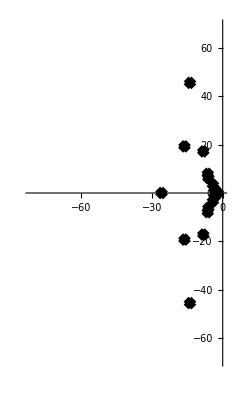

```mathematica
RootLocusPlot[1/Expand[ggr2[25524000,x]],{k,0,1},FeedbackType->None]
```

```mathematica
(1-1/List @@ NRoots[ggr2[25524000,x] == 0, x][[All, 2]])
```

{1.00514,1.00027-0.00185502 ⅈ,1.00027+0.00185502 ⅈ,1.00221-0.00766598 ⅈ,1.00221+0.00766598 ⅈ,1.03868,1.02554-0.0304718 ⅈ,1.02554+0.0304718 ⅈ,1.0061-0.0200984 ⅈ,1.0061+0.0200984 ⅈ,1.02258-0.0473686 ⅈ,1.02258+0.0473686 ⅈ,1.06122-0.0771102 ⅈ,1.06122+0.0771102 ⅈ,1.08099-0.0826102 ⅈ,1.08099+0.0826102 ⅈ,1.14421-0.118623 ⅈ,1.14421+0.118623 ⅈ,1.23313-0.111055 ⅈ,1.23313+0.111055 ⅈ,1.3438-0.0612693 ⅈ,1.3438+0.0612693 ⅈ,1.50299}

```mathematica
N[1/( 3 + I )]
```

0.3-0.1 ⅈ

```mathematica
N[1/(3 - 30I )]*N[1/(3 +30I )]
```

0.00110011+0. ⅈ

```mathematica
gg[100,z]
```

99+(6031 z)/60+(3167 z^2)/90+(3929 z^3)/720+(59 z^4)/180+(7 z^5)/720

```mathematica
gg2[n_,z_] := Expand[(gg[n,z]-(n-1))/z]
gg3[n_,z_] := Expand[(gg[n,z]/(n-1)-1)/z]
```

```mathematica
gg2[100,z]
```

6031/60+(3167 z)/90+(3929 z^2)/720+(59 z^3)/180+(7 z^4)/720

```mathematica
gg3[100,z]
```

6031/5940+(3167 z)/8910+(3929 z^2)/71280+(59 z^3)/17820+(7 z^4)/71280

```mathematica
Table[{n,gg2[n,z]-gg2[n-1,z]},{n,2,60}]//TableForm
```

2 | 0
3 | 0
4 | 1/2
5 | 0
6 | 1
7 | 0
8 | 5/6+z/6
9 | 1/2
10 | 1
11 | 0
12 | 3/2+z/2
13 | 0
14 | 1
15 | 1
16 | 13/12+(3 z)/8+z^2/24
17 | 0
18 | 3/2+z/2
19 | 0
20 | 3/2+z/2
21 | 1
22 | 1
23 | 0
24 | 11/6+z+z^2/6
25 | 1/2
26 | 1
27 | 5/6+z/6
28 | 3/2+z/2
29 | 0
30 | 2+z
31 | 0
32 | 77/60+(71 z)/120+(7 z^2)/60+z^3/120
33 | 1
34 | 1
35 | 1
36 | 2+(5 z)/4+z^2/4
37 | 0
38 | 1
39 | 1
40 | 11/6+z+z^2/6
41 | 0
42 | 2+z
43 | 0
44 | 3/2+z/2
45 | 3/2+z/2
46 | 1
47 | 0
48 | 25/12+(35 z)/24+(5 z^2)/12+z^3/24
49 | 1/2
50 | 3/2+z/2
51 | 1
52 | 3/2+z/2
53 | 0
54 | 11/6+z+z^2/6
55 | 1
56 | 11/6+z+z^2/6
57 | 1
58 | 1
59 | 0
60 | 5/2+2 z+z^2/2

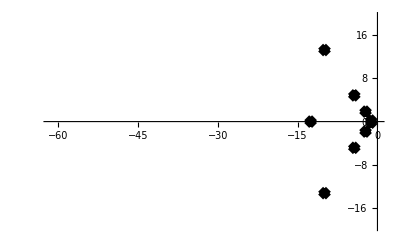

```mathematica
RootLocusPlot[1/Expand[ggr3[10000,x]],{k,0,1},FeedbackType->None]
```

```mathematica
(List @@ NRoots[ggr2[100,x] == 0, x][[All, 2]])
```

{-12.1997-12.3983 ⅈ,-12.1997+12.3983 ⅈ,-3.65742-1.85785 ⅈ,-3.65742+1.85785 ⅈ,-2.}

```mathematica
(List @@ NRoots[ggr3[100,x] == 0, x][[All, 2]])
```

{-11.1997-12.3983 ⅈ,-11.1997+12.3983 ⅈ,-2.65742-1.85785 ⅈ,-2.65742+1.85785 ⅈ,-1.}

```mathematica
(List @@ NRoots[ggr4[100,x] == 0, x][[All, 2]])
```

{-10.1997-12.3983 ⅈ,-10.1997+12.3983 ⅈ,-1.65742-1.85785 ⅈ,-1.65742+1.85785 ⅈ,0.}

```mathematica
vv:= {-11.199718313735842-12.398284753324173 ⅈ,-11.199718313735842+12.398284753324173 ⅈ,-2.6574245434070156-1.8578482376600212 ⅈ,-2.6574245434070156+1.8578482376600212 ⅈ,-1.}
```

99.+1.58392×10^-15 ⅈ

```mathematica
vv2:={-12.199718313735842-12.398284753324173 ⅈ,-12.199718313735842+12.398284753324173 ⅈ,-3.6574245434070143-1.8578482376600207 ⅈ,-3.6574245434070143+1.8578482376600207 ⅈ,-2.}
```

```mathematica
Product[ 1+1/j,{j,vv2}]99
```

28.5333+0. ⅈ

```mathematica
vv3:={-10.199718313735842-12.39828475332417 ⅈ,-10.199718313735842+12.39828475332417 ⅈ,-1.6574245434070143-1.857848237660022 ⅈ,-1.6574245434070143+1.857848237660022 ⅈ,0.}
```

```mathematica
Product[ 1-1/j,{j,vv3}](DD[100,-1]-1)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
(List @@ NRoots[ggr3[100,x] == 0, x][[All, 2]])
```

```mathematica
{-11.199718313735842-12.398284753324173 ⅈ,-11.199718313735842+12.398284753324173 ⅈ,-2.6574245434070156-1.8578482376600212 ⅈ,-2.6574245434070156+1.8578482376600212 ⅈ,-1.}
vv:= {-11.199718313735842-12.398284753324173 ⅈ,-11.199718313735842+12.398284753324173 ⅈ,-2.6574245434070156-1.8578482376600212 ⅈ,-2.6574245434070156+1.8578482376600212 ⅈ,-1.}
```

{-11.1997-12.3983 ⅈ,-11.1997+12.3983 ⅈ,-2.65742-1.85785 ⅈ,-2.65742+1.85785 ⅈ,-1.}

```mathematica
Product[ 1-1/j,{j,vv}]428/15
```

99.+1.58392×10^-15 ⅈ

```mathematica
Product[ (j-1)/j,{j,vv}]428/15
```

99.+0. ⅈ

```mathematica
Product[ 1+1/(j-1),{j,vv}]99
```

28.5333+0. ⅈ

```mathematica
Product[ (j)/(j-1),{j,vv}]99
```

28.5333+0. ⅈ

Power::infy: Infinite expression 1/0. encountered.

```mathematica
Product[ (j+1)/j,{j,vv}]428/15
```

0.+0. ⅈ

```mathematica
(List @@ NRoots[ggr3[100,x] == 0, x][[All, 2]])
```

{-11.1997-12.3983 ⅈ,-11.1997+12.3983 ⅈ,-2.65742-1.85785 ⅈ,-2.65742+1.85785 ⅈ,-1.}

```mathematica
(List @@ NRoots[ggr3a[100,x] == 0, x][[All, 2]])
```

NRoots::nnumeq: 720 + x\ (1 + x)\ (20544 + x\ (12034 + Times[« 2 »]))/720\ x == 0 is expected to be a polynomial equation in the variable x with numeric coefficients.

Part::partd: Part specification NRoots[720 + x\ (1 + x)\ (20544 + Times[« 2 »])/720\ x == 0, x] ⟦ All, 2 ⟧ is longer than depth of object.

{NRoots[(720+x (1+x) (20544+x (12034+x (2861+x (194+7 x)))))/(720 x)==0,x],All,2}

```mathematica
(List @@ NRoots[ggr3b[100,x] == 0, x][[All, 2]])
```

{-11.1997-12.3983 ⅈ,-11.1997+12.3983 ⅈ,-2.65742-1.85785 ⅈ,-2.65742+1.85785 ⅈ,-1.,0.}

```mathematica
(List @@ NRoots[ggr3e[100,x] == 0, x][[All, 2]])
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
vx:= {-11.199718313735842-12.398284753324173 ⅈ,-11.199718313735842+12.398284753324173 ⅈ,-2.6574245434070156-1.8578482376600212 ⅈ,-2.6574245434070156+1.8578482376600212 ⅈ,-1.,0.}
```

```mathematica
Sum[ If[ j == 0, 0, -1/j],{j,vx}]
```

1.58577+0. ⅈ

```mathematica
vy := {-11.199685576035794-12.398224487807218 ⅈ,-11.199685576035794+12.398224487807218 ⅈ,-2.6719503346754907-1.8618449055430242 ⅈ,-2.6719503346754907+1.8618449055430242 ⅈ,-0.9338092178222003,-0.03720467504094745}
```

```mathematica
Sum[ -1/j,{j,vy}]
```

28.5333+0. ⅈ

```mathematica
(List @@ NRoots[ggr3[200,x] == 0, x][[All, 2]])
```

{-14.9136-19.6281 ⅈ,-14.9136+19.6281 ⅈ,-3.99758-3.44993 ⅈ,-3.99758+3.44993 ⅈ,-1.21384-0.650558 ⅈ,-1.21384+0.650558 ⅈ}

```mathematica
vt:={-11.199718313735842-12.398284753324173 ⅈ,-11.199718313735842+12.398284753324173 ⅈ,-2.6574245434070156-1.8578482376600212 ⅈ,-2.6574245434070156+1.8578482376600212 ⅈ,-1.}
```

```mathematica
tt[s_] := 1+s(428/15) Product[ 1-s/j,{j,vt}]
```

```mathematica
tt[0]
```

1.+0. ⅈ

```mathematica
tv[z_] := 1+z(99) Product[ 1-(z-1)/(j-1),{j,vt}]
tv2[s_] := (99) Product[ 1+1/(j-1),{j,vt}]
```

```mathematica
tv2[4]
```

28.5333+0. ⅈ

```mathematica
(List @@ NRoots[ggr3f[100,x] == 0, x][[All, 2]])
```

{-12.1997-12.3982 ⅈ,-12.1997+12.3982 ⅈ,-3.67195-1.86184 ⅈ,-3.67195+1.86184 ⅈ,-1.93381,-1.0372}

```mathematica
(List @@ NRoots[ggr3e[100,x] == 0, x][[All, 2]])
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
vx:={-12.19968557603579-12.398224487807214 ⅈ,-12.19968557603579+12.398224487807214 ⅈ,-3.6719503346754956-1.8618449055430237 ⅈ,-3.6719503346754956+1.8618449055430237 ⅈ,-1.933809217822195,-1.0372046750409485}
```

```mathematica
Product[ 1-2/j,{j,vx}]100
```

1471.-8.88178×10^-14 ⅈ

```mathematica
Product[ 1+1/j,{j,vx}]100
```

1.+2.1684×10^-17 ⅈ

```mathematica
Product[ 1+3/j,{j,vx}]100
```

19.+1.38778×10^-15 ⅈ

```mathematica
Sum[ -1/(j),{j,vx}]
```

1.99517+0. ⅈ